```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework5

```mathematica
resistances={{10,0.748564},{20,0.767009},{30,0.770466},{40,0.771678}}
```

{{10,0.748564},{20,0.767009},{30,0.770466},{40,0.771678}}

```mathematica
Fit[resistances,{1,1/N^2},{N}]
```

0.773199-2.46406/N^2

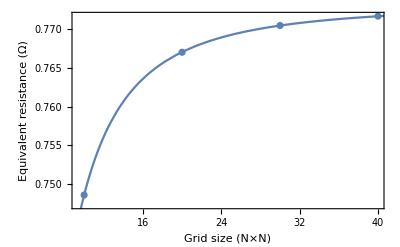

```mathematica
secondorder=Show[ListPlot[resistances], Plot[0.7731989100967313-2.464060593032833/x^2,{x, 0, 50}],Frame-> True,FrameLabel->{"Grid size (N×N)","Equivalent resistance (Ω)"} ]
```

```mathematica
Export["./3a.png",secondorder]
```

./3a.png

```mathematica
Fit[resistances,{1,1/N^2,1/N^4},{N}]
```

0.77324+3.29325/N^4-2.50052/N^2

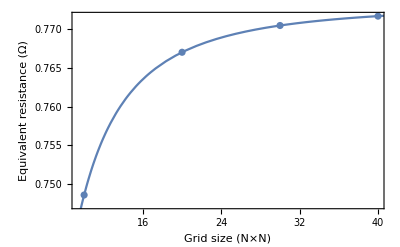

```mathematica
fourthorder=Show[ListPlot[resistances], Plot[0.7732398465128406+3.2932501866457065/x^4-2.5005175762315783/x^2,{x, 0, 50}], Frame->True, FrameLabel->{"Grid size (N×N)","Equivalent resistance (Ω)"}]
```

```mathematica
Export["./3b.png",fourthorder]
```

./3b.png

```mathematica
times={{10,0.030},{20,1.608},{30,18.108},{40,127.640}}
```

{{10,0.03},{20,1.608},{30,18.108},{40,127.64}}

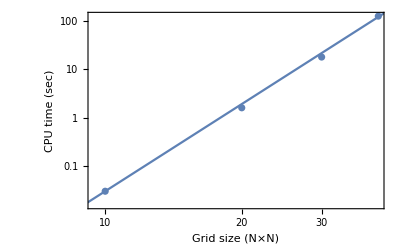

```mathematica
timegraph=Show[ListLogLogPlot[times],LogLogPlot[3*10^(-8) *x^6,{x,0,50}],Frame->True, FrameLabel->{"Grid size (N×N)","CPU time (sec)"}]
```

```mathematica
(Log10[127.64]-Log10[0.03])/(Log10[40]-Log10[10])
```

6.02742

```mathematica
Export["./time.png",timegraph]
```

./time.png

```mathematica
Fit[times,{N^6},{N}]
```

3.09666×10^-8 N^6